PrimeOmega gives how many multipled primes there are in total in a prime factorization.

```mathematica
FactorInteger@12
```

{{2,2},{3,1}}

The primes are 2, 3, the quantities are 2,1.

```mathematica
PrimeOmega@12
```

3

PrimeOmega is the sum of the quantities.

```mathematica
FactorInteger@327
```

{{3,1},{109,1}}

```mathematica
PrimeOmega@327
```

2

How many primes there are in the factorization itself can be inferred from the size of the resulting list.

```mathematica
FactorInteger@330
```

{{2,1},{3,1},{5,1},{11,1}}

```mathematica
Length@FactorInteger@330
```

4

Let’s create an index from the quantity of primes in a factorization together with the multiplicity of primes in the factorization, to create a rough “size” for each factorization.

```mathematica
Clear[FacSize];
FacSize=Function[{n},Length@FactorInteger@n*PrimeOmega@n];
```

```mathematica
{FacSize@12,FacSize@327,FacSize@330}
```

{6,4,16}

Which agrees with the prior observations.
Let’s plot the “factorization size” as a function of each integer:

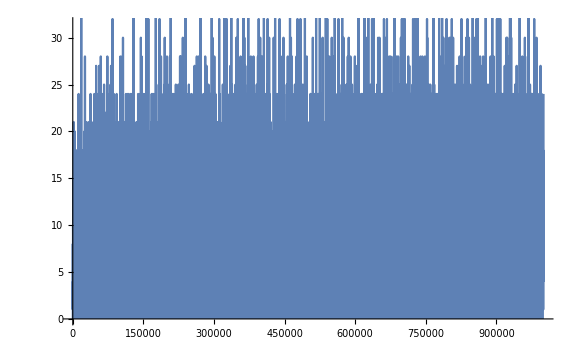

```mathematica
DiscretePlot[FacSize@x,{x,1,1000000,99},ExtentSize->Full]
```

This tells there is a ceiling of approximately 35.
If only the number of primes is plotted,

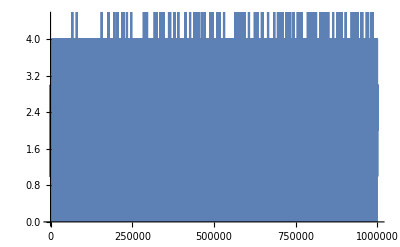

```mathematica
DiscretePlot[Length@FactorInteger@x,{x,1,1000000,99},ExtentSize->Full]
```

Let’s zoom in to the graph.

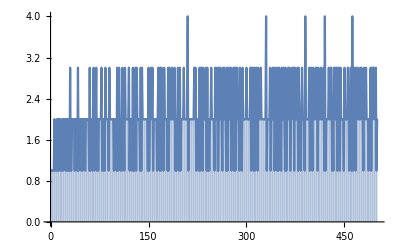

```mathematica
DiscretePlot[Length@FactorInteger@x,{x,1,500},ExtentSize->Full]
```

This seems to indicate no matter the size of the integer, there seems to be a clear upper bound on the size, by whatever estimate, of its prime factorization.

It is interesting to note that seemingly primes larger than the fifth prime, 11, are “useless”, in that they are not solicited by any factorization.

```mathematica
Prime@5
```

11